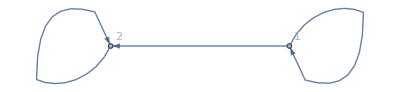

{{{1,y/(1-y)},{1/(1-y),0}},{{0,1/(1-y)}}}

{{1,y/(1-y)},{1/(1-y),0}}

r2∈ℝ&&0<y<1&&r1≤r2

```mathematica
x = DirectedGraph[{1->2, 2->2, 1->1}, VertexLabels->"Name"];
x (*Graph*)
frequencyVector[x] (*Entire frequency vector*)
fV = frequencyVector[x][[1]] (*Frequency vector of 1*)

frequencyToInequality[fV, r1]
```